```mathematica
(* Working N channel model

set directories  *)
```

```mathematica
nb1=NotebookOpen["~/Code/Nchannel/Nroutines.nb"];
```

```mathematica
SelectionMove[nb1,All,Notebook];
```

```mathematica
SelectionEvaluate[nb1];
```

```mathematica
NotebookClose[nb1];
```

```mathematica
SetDirectory["~/Code/NChannel/"]
```

/Users/mehtan/Code/Nchannel

```mathematica
(*energy grid for scattering problem *)
nk=2000;
ei=N[0.04];
ef=N[4.0];
ki=N[Log[ei]];
kf=N[Log[ef]];
dk=(kf-ki)/(nk-1);
kmat=Table[{Exp[ki+dk (k-1)],0},{k,nk}];
pmat=Table[{Exp[ki+dk (k-1)],0},{k,nk}];
qmat=Table[{Exp[ki+dk (k-1)],0},{k,nk}];
amps=Table[{Exp[ki+dk (k-1)],0},{k,nk}];
usig=Table[{kmat[[k,1]],4 π/(2kmat[[k,1]])},{k,nk}];
(* establish the model potential *)

R=10;
m=1.0;
L=0;
n=100;
d=10.0; (* depth of all channels *)
c=2.0; (* coupling*)
delta=10.00; (* closed threshold *)
nc=n-1;
io=n;
ampsfull=Table[0,{i,nk},{j,nc}];

(* drawing psi grid *)
xi=0;
xf=1.5 R;
ks=√(2 m (d+c+ef))/(2 π) ; (* largest wave number *)
xx=(xf-xi)ks 15;
nx=xx-Mod[xx,1];
dx=(xf-xi)/(nx-1);
nx
(*dx=0.1;nx=(xf-xi)/dx;*)

xmat=Table[xi+(i-1) dx,{i,nx}];
psimat=Table[0,{i,n nx}];

decay[k_,x_]:=bg[L,k,x-R+1];
ddecay[k_,x_]:=dbg[L,k,x-R+1];

(*defines: U, UT, Ve ]*)

DefinePotential[1,n,c,d,delta]
MatrixForm[U];
Ve;
```

202.

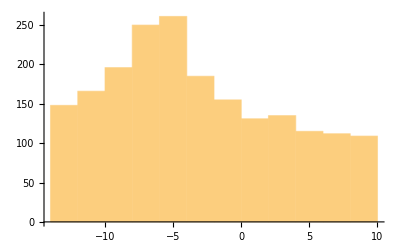

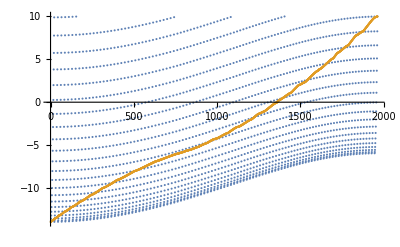

```mathematica
(* find dos *)
findroots[R,L,Ve,delta] (* result ={nroots,roots} get the bessel roots for DOS arguments *)

hh=Table[100,{i,nroots n}];
h5=Table[0,{i,nroots n}];
q=0;
qs=0;
etop=Min[4 ef,delta] ;
Do[e0=Ve[[i]];
Do[ee=roots[[j]]+e0;If[ei<ee&&ee<ef,qs=qs+1;h5[[qs]]=ee;]
If[ee<etop,q=q+1;hh[[q]]=ee;,Break[]];,{j,nroots}];
,{i,n}];
h2=Sort[hh];
h3=Table[h2[[i]],{i,q}];
h4=Table[hh[[i]],{i,q}];
Histogram[h3]
 ListPlot[{h4,h3}]

L (L+1)/(2 m R^2);
```

```mathematica
DefinePotential[1,n,c,d,delta]
start = SessionTime[];
ptime=0;
stime=0;ip=250;

ik=30;
En=0.7093622471849472;
(*En=1.155554296086053;kmat[[ik,1]];*)
(* interior wavefunctions *)
ke=Table[N[√(2 m (En-Ve[[i]]))],{i,n}];
phi[x_]=Table[If[En-Ve[[i]]>0,f[0,ke[[i]],x] ,bf[0,Im[ke[[i]]],x]]KroneckerDelta[i,j],{i,n},{j,n}];
dphi[x_]=Table[If[En-Ve[[i]]>0,df[0,ke[[i]],x] ,dbf[0,Im[ke[[i]]],x]] KroneckerDelta[i,j],{i,n},{j,n}];
ko=N[√(2 m (En))];
kc=N[√(2 m(delta-En))]; 
 t1=SessionTime[];

scattering[ko,kc,phi,dphi];(* produce: coef, aclose, sd, cd, phase, phi, dphi *)
phase=ArcTan[sd/cd];
sig=4 π Sin[phase]^2/ko^2;
kmat[[ik,2]]=sig;
pmat[[ik,2]]=phase/π;

 t2=SessionTime[];

stime=stime+(t2-t1);

makePSI[ko,kc,U,phi,dphi,coef,aclose,cd,sd];  (* psimat defined *)
ampsfull[[ik]]=Table[ dx Sum[psimat[[i+nx (it-1)]]^2,{i,nx}],{it,nc}];
amps[[ik,2]]= Sum[ampsfull[[ik,it]],{it,nc}];
```

```mathematica
hold=Table[0,{i,nx},{it,n+1}];
Do[hold[[i,1]]=xmat[[i]],{i,nx}];
Do[hold[[i,it+1]]=psimat[[i+nx (it-1)]],{i,nx},{it,n}];
Export["psi02.dat",hold,"Table"];
```

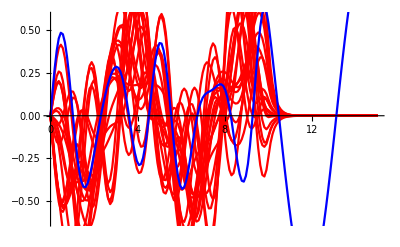

```mathematica
Plots=Table[0,{i,n}];
CPlots=Table[0,{i,nc}];
Do[
hold=Table[{xmat[[i]],psimat[[i+nx (it-1)]]},{i,nx}];
If[it==io,
Plots[[it]]=ListPlot[hold,PlotStyle->Blue,PlotRange->All,Joined->True];
,
Plots[[it]]=ListPlot[hold,PlotStyle->Red,PlotRange->All,Joined->True];
CPlots[[it]]=ListPlot[hold,PlotStyle->Red,PlotRange->All,Joined->True];
]
,{it,n}]
Show[Plots]
Show[CPlots];
```

```mathematica
qmat=pmat;
hold=Table[{0,0,0},{i,nk}];
isum=5;
(* smooth data so you can add pi to it *)
Do[e1=Sum[qmat[[ik-j,2]],{j,0,isum-1}]/isum;
If[ik<nk-isum,e2=Sum[qmat[[ik+j,2]],{j,isum}]/isum;];
If[e2-e1>0.65,Do[qmat[[j,2]]=qmat[[j,2]]-1,{j,ik+1,nk}];];
,{ik,1+isum,nk}];

(* formatted write out for scattering and amplitude *)
out=Table[{0,0,0,0},{i,nk+2}];
out[[1,1]]="# n=";
out[[1,2]]={n," R=",R," delta=",delta};
out[[1,3]]={"d=",d," c=",c};
out[[2,1]]="# energy";
out[[2,2]]="sigma";
out[[2,3]]="closed channel amplitude";
out[[2,4]]="phase";
Do[out[[i+2]]={kmat[[i,1]],kmat[[i,2]],amps[[i,2]],qmat[[i,2]]},{i,nk}];
str1="result";str2=ToString[n];str3=".dat";
If[L==0,file=str1<>str2<>str3;,
str4="L";str5=ToString[L];
file=str1<>str2<>str4<>str5<>str3;
]
Export[file,out,"Table"]
str1="amp";str2=ToString[n];str3=".dat";
If[L==0,file=str1<>str2<>str3;,
str4="L";str5=ToString[L];
file=str1<>str2<>str4<>str5<>str3;
]
out=Table[0,{i,nk},{j,n}];
Do[out[[i,1]]=kmat[[i,1]];
Do[out[[i,j+1]]=ampsfull[[i,j]],{j,nc}];
,{i,nk}];
Export[file,out,"Table"]
```

result20.dat

amp20.dat

```mathematica
(*/amps[[i,2]]*)
```

```mathematica
(*out2=Table[out[[i,j]],{j,n},{i,nk}];
ListContourPlot[out2]*)
```